===============================================================================

Dalam menjawab soal-soal berikut, diasumsikan bahwa orang awam adalah orang-orang dengan kemampuan matematika yang cukup, yakni setidaknya memiliki pemahaman atas fungsi kartesius, fungsi polar, dan integral serta berkeinginan untuk mempelajari atau menerapkan Wolfram Mathematica.

===============================================================================
===============================================================================

#### Bookmarks

===============================================================================
===============================================================================

#### Introduction

1. Cara membuat fungsi
2. Cara membuat fungsi yang memiliki parameter
3. Data Array
4. Fungsi built-in Print dan Range
5. Fungsi built-in Module, For, dan Plot serta Show
6. Fungsi built-in Manipulate dan Animate
7. Fungsi built-in N, Sqrt, Total, Expand, dan Solve
8. Fungsi built-in Out
9. Fungsi built-in Clear
10. Tentang Comment

------------------------------------------------------------------------------------------------------------------------------------------

1. Cara membuat fungsi

Fungsi dibuat menggunakan “:=”
Misalkan:

```mathematica
x=2;
```

Dengan ini, kita telah mendefinisikan sebuah input x sebagai bernilai 2.
“;” berfungsi agar menjalankan program namun tidak menampilkan hasil.
Selanjutnya, kita akan buat contoh sebuah fungsi polinomial berisikan x:

```mathematica
P:=x^2+2x+1;
```

Dengan ini, kita telah membuat fungsi P.
Bila kita panggil fungsi P:

```mathematica
P
```

9

Maka kita akan dapatkan sesuai input nilai x yaitu 2 nilai P = 2^2+2*2+1= 4 + 4 + 1 = 9

------------------------------------------------------------------------------------------------------------------------------------------

2. Cara membuat fungsi yang memiliki parameter
Kita akan definisikan ulang fungsi yang sebelumnya menjadi P_1 dimana P_1 merupakan fungsi yang memiliki parameter:

```mathematica
P1[x_]:=x^2+2x+1;
```

Parameter di sini memaksudkan bahwa saat kita panggil fungsi ini dengan menggantikan nilai parameternya sesuai input, akan muncul hasil yang diinginkan. Mari kita panggil fungsi ini dengan x = 2 seperti sebelumnya:

```mathematica
P1[2]
```

9

Apa perbedaannya melakukan ini dengan cara yang sebelumnya?
Pada cara yang sebelumnya, kita terlebih dahulu harus mendefinisikan sebuah input x barulah mendefinisikan sebuah fungsi x yang nilainya digantikan oleh input x tersebut. Namun ini tidak efisien dikarenakan kita harus mendefinisikan ulang input x apabila ingin mengganti input x tersebut. Dengan fungsi yang langsung memetakan parameter x, maka hanya perlu memanggil fungsi beserta menggantikan parameter sesuai yang diinginkan, sehingga tidak perlu melakukan pendefinisian ulang input x kemudian kembali melakukan panggilan fungsi.

Suatu fungsi tidak terbatas pada satu parameter, namun bisa banyak parameternya. Sebagai contoh:

```mathematica
P2[x_,y_,z_]:=(x+y-z)^2+2(x-y+z)-y-z;
```

Mari kita panggil fungsi ini dengan sembarang bilangan x, y, z. Misal x = 3, y = 2, z = 1

```mathematica
P2[3,2,1]
```

17

Fungsi tersebut memetakan sesuai parameter dan mencari parameter tersebut dalam fungsi dan menggantikan nilainya dengan input.
Sesuai input: x = 3, y = 2, z = 1, maka yang bekerja dalam pemanggilan fungsi ini adalah:
(3 + 2 - 1)^2+2(3 - 2 + 1) - 2 - 1 = 4^2 + 2*2 - 3 = 16 + 4 - 3 = 17

------------------------------------------------------------------------------------------------------------------------------------------

3. Mengenai Data Array

Array adalah salahsatu tipe data yang berupa kumpulan-kumpulan data. Misal:

```mathematica
A={1,4,6};
```

Misal kita ingin mengambil data 4 dari array A. Karena 4 adalah elemen kedua dari A, maka panggil dengan:

```mathematica
A[[2]]
```

4

Kita juga dapat mengubah nilai dalam array tersebut. Misal angka 4 kita ingin ubah dengan kata “Empat”.

```mathematica
A[[2]]="Empat";
A
```

{1,Empat,6}

------------------------------------------------------------------------------------------------------------------------------------------

4. Mengenai Fungsi Print dan Range

- Fungsi Print adalah sebuah fungsi yang menunjukkan output

```mathematica
Print[4+6]
```

10

- Fungsi Range adalah sebuah fungsi yang membuat sebuah array dari suatu interval.
Misal kita ingin membuat array berisi 1 hingga 5.

```mathematica
Range[1,5]
```

{1,2,3,4,5}

Parameter pertama adalah batas bawah dan parameter kedua adalah batas atas.

Range bisa berisi hanya 1 parameter saja. Secara default, rangenya didefinisikan untuk dimulai dari 1 sehingga contoh sebelumnya dapat dikerjakan dengan:

```mathematica
Range[5]
```

{1,2,3,4,5}

Range bisa berisi 3 parameter, parameter ketiga sebagai lompatan. Secara default, lompatan adalah 1. Misal kita ingin membuat bilangan ganjil kurang dari 10.

```mathematica
Range[1,10,2]
```

{1,3,5,7,9}

------------------------------------------------------------------------------------------------------------------------------------------

5. Mengenai Fungsi Module, For, dan Plot serta Show
- Fungsi Module adalah sebuah fungsi yang memungkinkan untuk melakukan fungsi-fungsi secara lokal.
Lokal di sini maksudnya adalah variabel dan fungsi yang ada pada lokal hanya bekerja secara internal.
Input x = 2 seperti sebelumnya merupakan Global.
Mungkin agak sulit untuk dimengerti dengan penjelasan seperti ini, maka perhatikan sebuah contoh berikut.
Misalkan G[x, y] sebuah fungsi yang akan menghasilkan output Jumlah dan Selisih dari x dan y.
Maka kita perlu membuat suatu Module dalam fungsi G[x, y] di mana parameternya adalah Jumlah dan Selisih.

```mathematica
G[x_,y_]:=
Module[
{Jumlah, Selisih},
Jumlah = x + y;
Selisih = Abs[x - y];
Print["Jumlah dari x dan y adalah: ", Jumlah];
Print["Selisih dari x dan y adalah: ", Selisih]
]
```

(catatan: Abs di sini berarti Absolute atau Mutlak. Mengapa demikian? Karena kita tidak mengetahui apakah nilai x atau y yang akan menjadi input yang lebih besar, maka karena kita mencari selisihnya di mana nilai selisih kita inginkan selalu bernilai tak negatif, maka kita gunakan fungsi mutlak atau Absolute)

Mari kita panggil fungsi ini dengan sembarang nilai x dan y, misal x = 2 dan y = 5.

```mathematica
G[2,5]
```

Jumlah dari x dan y adalah: 7

Selisih dari x dan y adalah: 3

- Fungsi For adalah fungsi iterasi yang melakukan pengulangan secara secara berurutsesuai step (naikan) yang kita definisikan untuk menghasilkan output secara berurut.
Sebagai contoh, kita akan buat sebuah fungsi yang mencetak (men-print) angka 1 hingga 5.

```mathematica
Prt :=For[i=1,i≤ 5,i++,Print[i]];
```

Fungsi tersebut dibaca sebagai: “Kita menset i sebagai 1. Maka selama i bernilai kurang lebih atau sama dengan 5 dengan step 1 (i++ berarti i = i + 1), maka akan di-print i.”
Mari kita jalankan fungsi tersebut.

For sangat berguna saat kita memerlukan melakukan pengulangan dalam suatu fungsi secara berurut.

- Fungsi Plot adalah fungsi yang membuat sketsa atau plotting dari suatu fungsi.
Sebagai contoh, mari kita sketsakan fungsi x^2:

```mathematica
Plt:=Plot[x^2,{x,-3,3},PlotRange->{0,10}];
```

Fungsi tersebut dibaca sebagai “Sketsakan x^2 dimana gambar difokuskan pada x di interval -3 hingga 3 dan pada y di interval 0 hingga 10”.
Mengapa y demikian? Karena x^2 selalu bernilai tak negatif.
Mari kita panggil fungsi tersebut.

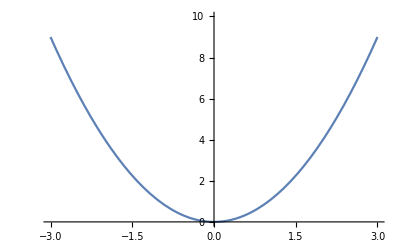

```mathematica
Plt
```

Apabila hanya begini saja, kurang menarik untuk dilihat.
Dapat dilakukan beberapa modifikasi terhadap plot sehingga akan tampak lebih enak dipandang.
Sebagai contoh, kita akan mengatur ketebalan atau Thickness menggunakan PlotStyle dan memberikan label pada fungsi tersebut menggunakan PlotLegends.

```mathematica
Plt1:=Plot[
x^2,{x,-3,3},
PlotRange->{0,10},
PlotStyle->Thickness[0.01],
PlotLegends->"Expressions"];
```

Mengenai Thickness, tidak ada cara pasti untuk menentukan sebuah angka agar ketebalan tepat sesuai yang diinginkan. Coba kreasikan saja berkali-kali hingga mendapatkan hasil yang diinginkan.
Mengenai Legends, Expressions merupakan salahsatu cara membubuhkan label. Ada beberapa cara seperti Automatic atau bahkan pengaturan penempatan. Baca saja documentationnya mengenai hal tersebut.
(Documentation merupakan alat yang sangat kuat karena dapat membantu menjadikan pekerjaanmu lebih maksimal. Documentation dapat diakses melalui Help > Documentation Center atau cara yang lebih enak adalah dengan mengetik suatu fungsi tidak sampai habis dan menklik tanda garis tiga yang akan muncul di sampingnya)

Sekarang mari kita panggil fungsi tersebut.

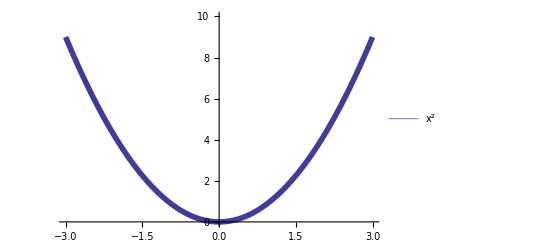

```mathematica
Plt1
```

Nah sekarang sudah lebih enak dilihat. Apabila ditunjukkan pada orang lain, mereka akan langsung paham bahwa disketsa sebuah grafik x^2 yang terlihat jelas karena telah ditebalkan.

- Fungsi Show adalah fungsi untuk memerlihatkan satu atau lebih grafik yang diciptakan melalui Plot atau Graphics. Sebagai contoh, kita dapat memerlihatkan fungsi sebelumnya dengan sebagai berikut:

```mathematica
Show[Plt1]
```

-Graphics-

------------------------------------------------------------------------------------------------------------------------------------------

6. Mengenai Fungsi Manipulate dan Animate

Manipulate dan Animate ini adalah fungsi-fungsi yang dapat digunakan untuk mengiterasikan sebuah variabel bebas dari sesuatu yang ingin dikerjakan.
Sebagai contoh, kita dapat gunakan ini untuk menghasilkan Plot yang dapat berubah-ubah nilainya.

```mathematica
{Manipulate[Plot[Sin[a x],{x,0,2π}],{a,0,5}],
Animate[Plot[Sin[a x],{x,0,2π}],{a,0,5},AnimationRunning->False]}
```

{,}

Ada beberapa perbedaan antara Manipulate dan Animate.
Hal mendasarnya adalah Manipulate lebih lengkap dan dapat menspesifikasi nilai tepat variabel bebas yang diinginkan.
Animation lebih untuk membuat Animasi. Kita bisa buat animasi berjalan lebih cepat, nilai variabel bebas berubah sesuai lompatan, dan sebagainya.
Secara lengkapnya, bisa dilihat di documentation masing-masing fungsi tersebut.

------------------------------------------------------------------------------------------------------------------------------------------

7. Mengenai fungsi N, Sqrt, Total, dan Expand

- Fungsi N adalah fungsi yang mengubah isinya menjadi bentuk desimalnya. Misal:

```mathematica
10/3
```

10/3

ini berbentuk sebuah pecahan. Kita dapat ubah ini menjadi bentuk desimal dengan:

```mathematica
N[10/3]
```

3.33333

- Fungsi Sqrt adalah singkatan untuk SquareRoot, artinya akar kuadrat. Misalkan kita ingin mencari nilai dari √4, maka:

```mathematica
Sqrt[4]
```

2

- Fungsi Total adalah fungsi yang menjumlahkan semua elemen dari sebuah array. Misal:

```mathematica
Total[{1,2,3}]
```

6

- Fungsi Expand adalah fungsi yang mengekspansikan ekspresi. Misal kita ingin tulis (y+2)^2 sebagai ekspansi kuadratnya, maka:

```mathematica
Expand[(y+2)^2]
```

4+4 y+y^2

- Fungsi Solve adalah fungsi yang dapat menyelesaikan persamaan-persamaan yang kita punya. Misal kita ingin mencari solusi dari:

4p+2q=2
3p-2q=5

```mathematica
Solve[4p+2q==2&&3p-2q==5,{p,q}]
```

{{p→1,q→-1}}

------------------------------------------------------------------------------------------------------------------------------------------

8. Mengenai fungsi Out

Out berguna untuk memanggil output dari sebuah proses yang sebelumnya dikerjakan. Misal kita ingin mengambil output dari ekspansi (y+2)^2 pada contoh sebelumnya. Maka:

```mathematica
Out[29]
```

4+4 y+y^2

Untuk memanggil output yang paling terakhir, maka kita bisa menggunakan %.

```mathematica
%
```

4+4 y+y^2

------------------------------------------------------------------------------------------------------------------------------------------

9. Mengenai Fungsi Clear
Sebelum kita beralih dari suatu pekerjaan ke pekerjaan lain, kita pasti telah menggunakan variabel-variabel yang kemungkinan akan bertabrakan dengan yang akan digunakan pada pekerjaan-pekerjaan berikutnya. Maka kita hilangan variabel tersebut menggunakan Clear.
Sebagai contoh, mari kita panggil x:

```mathematica
x
```

2

Maka apabila kita membuat fungsi yang melibatkan x, akan bertabrakan dengan input yang telah diberikan.
Maka kita akan hilangkan input nilai x dengan cara:

```mathematica
Clear[x]
```

Mari kita coba panggil kembali x.

```mathematica
x
```

x

Maka x sudah tidak bernilai.

Ada juga fungsi clear yang dapat menghapus lebih dari satu variabel sekaligus yaitu ClearAll.
Mari kita hapus semua variabel yang digunakan pada introduction ini.

```mathematica
ClearAll[P,P1,P2,A,G,Prt,Plt,Plt1]
```

Jika variabelnya berwarna biru, maka variabelnya belum terdefinisi.
Jika variabelyna berwarna hitam, maka variabelnya  terdefinisi dengan suatu nilai.

-------------------------------------------------------------------------------------------------------------------------------------------------

10. Mengenai Comment

Kita bisa membuat komen pada kode. Komen di sini bisa ditaruh di tengah kode dan tidak akan dijalankan.
Syntaxnya adalah (*...*)
Misal:

```mathematica
Print[5^2(*Ini adalah komen, tidak dijalankan oleh kode*)]
```

25

-------------------------------------------------------------------------------------------------------------------------------------------------

Sekarang mari kita jawab soal nomor 1

===============================================================================
===============================================================================

#### Nomor 1

1. Diberikan gambar grafik sebagai berikut
-Graphics-
a. Carilah fungsi yang memenuhi gambar plot diatas!
b. Gambarkan fungsi yang anda temukan pada soal a. dalam PolarPlot!
c. Carilah luas daerah yang diarsir!

------------------------------------------------------------------------------------------------------------------------------------------

a. Akan ditentukan fungsi yang memenuhi gambar plot di atas

Perhatikan bahwa fungsi tersebut adalah fungsi persamaan kuadrat, sehingga pertama definisikan fungsi tersebut sebagai f(x)=ax^2+bx+c.
Sekarang kita akan tentukan nilai-nilai dari a, b, dan c.

#### Cara 1: Menggunakan Analisis Gambar Fungsi

Perhatikan bahwa fungsi tersebut terbuka ke bawah, artinya a pasti bernilai negatif.
Selanjutnya perhatikan kita punya tiga buah titik dari fungsi tersebut, yaitu (-1.5,0),(2,0),(0,6)
Artinya fungsi tersebut pasti memiliki faktor (-1),(x-(-1.5)), dan (x-2).
Namun jika fungsinya adalah f(x)=-(x+1.5)(x-2), maka saat x=0, maka f(x)=3 sehingga kalikan fungsi tersebut dengan 2.
∴ f(x)=-2(x+1.5)(x-2)

#### Cara 2: Menggunakan Sistem Persamaan Linier Tiga Variabel

Substitusikan titik-titik yang kita punya yaitu (-1.5,0),(2,0),(0,6) ke persamaan f(x)=ax^2+bx+c, maka akan kita peroleh:

2.25a-1.5b+c=0
            4a+2b+c=0
                                    c=6

Kita dapat gunakan solve untuk memperoleh solusinya.

```mathematica
Solve[2.25a-1.5b+c==0&&4a+2b+c==0&&c==6,{a,b,c}]
```

{{a→-2.,b→1.,c→6.}}

Substitusikan kembali hasil solve maka kita peroleh f(x)=ax^2+bx+c=-2 x^2+x+6.
∴f(x)=-2 x^2+x+6

Kita dapat mengecek hasil-hasil ini dengan menggunakan interpolasi dan memasukkan data titik-titik yang kita punya.

```mathematica
InterpolatingPolynomial[{{-1.5,0},{2,0},{0,6}},x]
```

-2. (-2+x) (1.5+x)

```mathematica
Print["Fungsinya adalah "  <> ToString[Expand[%]//TraditionalForm]]
```

Fungsinya adalah -2. x^2+1. x+6.

Sekarang mari kita plot fungsi yang kita peroleh

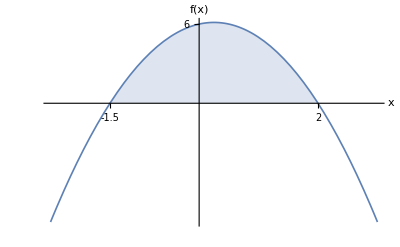

```mathematica
Plot[{-2 x^2+x+6,Which[-1.5≤x≤2,0]},{x,-2.5,3},
PlotStyle->{{Thickness[0.003]},Transparent} ,Ticks->{{-1.5,2},{6}},
AxesLabel->{"x","f(x)"},Filling->{1->{2}},Background->White
]
```

Dengan ini, soal nomor 1 bagian a telah terjawab.

b. Akan digambarkan fungsi f(x)=-2(x+1.5)(x-2) dalam koordinat polar

Untuk mengubah fungsi f(x) dari koordinat kartesius menjadi koordinat polar, gunakan x=r cos(θ) dan f(x)=r sin(θ), sehingga:

f(x)=-2 x^2+x+6
                                                                 r sin(θ)=-2 r^2 cos^2(θ)+r cos(θ)+6
 2 r^2 cos^2(θ)-r cos(θ)+r sin(θ)-6=0
2cos^2(θ)r^2-(cos(θ)-sin(θ))r -6=0

Kita juga dapat menggunakan fungsi built-in yaitu TransformedField. Spesifikasikan bahwa kita ingin mengubah dari kartesius menjadi polar. Ubah dahulu fungsi f(x)=-2 x^2+x+6 menjadi f(x)+2 x^2-x-6=0. Misal y=f(x). Sehingga:

```mathematica
TransformedField["Cartesian"->"Polar",y+2 x^2-x-6,{x,y}->{r,θ}]
```

-6-r Cos[θ]+2 r^2 Cos[θ]^2+r Sin[θ]

Kita dapat mengecek hasil ini dengan hasil sebelumnya.

```mathematica
%===Expand[2 Cos[θ]^2 r^2-(Cos[θ]-Sin[θ])r-6]
```

True

Sehingga benar bahwa 2cos^2(θ)r^2-(cos(θ)-sin(θ))r -6=0 adalah fungsi dalam koordinat polar dari f(x)=-2 x^2+x+6. Namun ini belum selesai karena yang kita cari adalah persamaan r=h(θ).
Cari solusi untuk r dengan menggunakan solve dari persamaan yang kita peroleh.

```mathematica
Solve[2(Cos[θ])^2 r^2-(Cos[θ]-Sin[θ])r-6==0,r]
```

{{r→1/4 Sec[θ]^2 (Cos[θ]-Sin[θ]+√(25+24 Cos[2 θ]-Sin[2 θ]))},{r→1/4 (Sec[θ]-Sec[θ]^2 √(25+24 Cos[2 θ]-Sin[2 θ])-Sec[θ] Tan[θ])}}

Selanjutnya mari kita plot fungsi yang kita peroleh.

```mathematica
R=%[[All,1,2]];(*Mengubah array solusi menjadi himpunan fungsi r*)
```

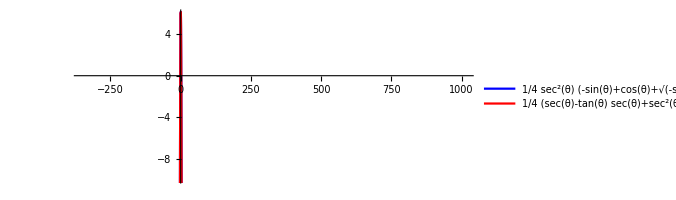

```mathematica
PolarPlot[{R[[1]],R[[2]]},{θ,0,2π},
PlotStyle->{Blue,Red},PlotRange->{-10,6},PlotLegends->{R[[1]],R[[2]]}]
```

Kedua fungsi tersebut hampir sama pada 0≤θ≤2π. Namun kita dapat menggunakan Manipulate untuk melihat proses penggambarannya.

```mathematica
Manipulate[PolarPlot[{R[[1]],R[[2]]},{θ,0,a},
PlotStyle->{Blue,Red},PlotRange->10,PlotLegends->{R[[1]],R[[2]]}],{a,0.0001,2π}, ContentSize->{800,300}]
```

Terlihat bahwa walaupun gambar akhirnya hampir sama pada interval 0≤θ≤2π, namun tidak demikian pada interval 0≤θ≤a untuk sebagian besar 0.0001≤a≤2π.

Dengan ini, soal nomor 1 bagian b telah terjawab.

c. Akan ditentukan luas daerah yang diarsir

Pertama, mari kita lihat kembali gambar fungsi tersebut agar kita mendapatkan gambaran untuk menghitung luas daerah yang diarsir.

```mathematica
Out[4]
```

-Graphics-

Untuk mencari luas daerah antara fungsi tersebut dan sumbu x pada -1.5≤x≤2, maka integrasikan fungsi tersebut pada interval tersebut.

```mathematica
Integrate[-2 x^2+x+6,{x,-1.5,2}]
```

14.2917

∴ Luas daerah yang diarsir adalah sebesar 14.2917 satuan luas.

Dengan ini, soal nomor 1 bagian c telah terjawab.

Maka dengan ini, soal nomor 1 telah terjawab.

Mari kita hapus variabel-variabel yang telah kita definisikan agar tidak mengganggu nomor-nomor selanjutnya.

```mathematica
ClearAll[R]
```

===============================================================================
===============================================================================

#### Nomor 2

2. Diberikan persamaan polar r=2a sin(kθ),r=2a cos(kθ),r=2a sin(kθ)+b,r=2a cos(kθ)+b
a. Gambarkan setiap persamaan polar di atas dengan Manipulate/Animate
b. Jelaskan secara detail hubungan a dan k pada persamaan polar r=2a sin(kθ),r=2a cos(kθ) (jika a makin besar dan k konstan, jika k makin besar,
    jika a≠k, jika a=k, semua kombinasi a (Positif atau negatif) dan k (Positif atau negatif), dan lain-lain)
c. Jelaskan pengaruh b pada persamaan polar r=2a sin(kθ)+b,r=2a cos(kθ)+b

------------------------------------------------------------------------------------------------------------------------------------------

a. Akan digambarkan setiap persamaan-persamaan polar tersebut dengan menggunakan Manipulate.

Metodologi penggambaran yang digunakan di sini memisahkan fungsi r yang bergantung pada b dan yang tidak bergantung pada b.
Mari kita pertama gambarkan fungsi-fungsi r yang tidak bergantung pada b.

```mathematica
{Manipulate[Show[
Plot[,{x,-2π,2π},Axes->True,Ticks->{
{{-2a,-2a},{-a,-a},{a,a},{2a,2a}},
{{-2a,-2a},{-a,-a},{a,a},{2a,2a}}},
PlotRange->2π,AspectRatio->Full,PlotLabel->r==2a Sin[k θ]],(*Untuk mengubah ticks kartesius*)
PolarPlot[2 a Sin[k θ],{θ,0,2π}]],{a,-3,3},{k,-2,2},
ContentSize->{300,300}],
Manipulate[Show[
Plot[,{x,-2π,2π},Axes->True,Ticks->{
{{-2a,-2a},{-a,-a},{a,a},{2a,2a}},
{{-2a,-2a},{-a,-a},{a,a},{2a,2a}}},
PlotRange->2π,AspectRatio->Full,PlotLabel->r==2a Cos[k θ]],
PolarPlot[2 a Cos[k θ],{θ,0,2π}]],{a,-3,3},{k,-2,2},
ContentSize->{300,300}]}
```

{,}

Sekarang mari gambarkan fungsi-fungsi r yang bergantung pada b.

```mathematica
{Manipulate[PolarPlot[2 a Sin[k θ]+b,{θ,0,2π},PlotRange->8,PlotLabel->r==2a Sin[k θ]+b],{a,-3,3},{k,-2,2},{b,-10,10},
ContentSize->{300,300}],
Manipulate[PolarPlot[2 a Cos[k θ]+b,{θ,0,2π},PlotRange->8,PlotLabel->r==2a Cos[k θ]+b],{a,-3,3},{k,-2,2},{b,-10,10},
ContentSize->{300,300}]}
```

{,}

Dengan ini, soal nomor 2 bagian a telah terjawab.

b. Akan dijelaskan hubungan a dan k pada persamaan-persamaan r=2a sin(kθ),r=2a cos(kθ)

Mari kita panggil ulang gambar kedua persamaan tersebut terlebih dahulu.

```mathematica
Out[14]
```

{,}

Perhatikan bahwa persamaan-persamaan tersebut merupakan persamaan-persamaan polar untuk mawar.
- Jelas bahwa a mengatur ukuran dari grafik yang dibentuk.
- k mengatur bentuk fungsi yang dibentuk. Jika k bukan bilangan bulat, maka k membuat persamaan-persamaan tersebut bukanlah mawar namun 
  sembarang persamaan fungsi dalam koordinat polar. Jika k adalah bilangan bulat, maka:
  1. Jika k ganjil, jumlah mawar yang dibentuk adalah k, kasus khusus jika k=±1, dimana:
      a. Jika k=1, maka fungsi yang terbentuk adalah fungsi lingkaran yang berpusat di (-a,0) untuk r=2a cos(θ) dan (0,-a) untuk r=2a sin(θ)
      b. Jika k=-1, maka fungsi yang terbentuk adalah fungsi lingkaran yang berpusat di (-a,0) untuk r=2a cos(-θ) dan (0,a) untuk r=2a sin(θ)
          Pusat lingkaran tidak berpengaruh untuk r=2a cos(kθ) karena cos(x)=cos(-x),∀x∈ℝ.
  2. Jika k genap, jumlah mawar yang dibentuk adalah 2k.

Dengan ini, soal nomor 2 bagian b telah terjawab.

c. Akan dijelaskan pengaruh b pada persamaan-persamaan r=2a sin(kθ)+b,r=2a cos(kθ)+b

Mari kita panggil ulang gambar kedua persamaan tersebut terlebih dahulu.

```mathematica
Out[15]
```

{,}

Jika b=0, maka kembali ke kasus sebelumnya.
Jika b≠0, maka:
A. Untuk r=2a Sin[kθ]+b
1. Jika b<0, maka daun yang berada di kuadran I dan kuadran IV akan masuk ke dalam hingga hilang menyeluruh pada b=-2a dan daun yang berada di 
    kuadran II dan kuadran III akan membesar. Saat b<-2a, semakin kecil nilai b maka kedua daun tersebut akan semakin melebar menjauhi titik asal.
2. Jika b>0, akan berlaku sebaliknya. Daun yang berada di kuadran I dan IV akan melebar dan daun yang berada di kuadran II dan III akan masuk ke 
    dalam hingga hilang menyeluruh pada b=2a. Saat b>2a, semakin besar nilai b maka kedua daun tersebut akan semakin melebar menjauhi titik asal.
B. Untuk r=2a Cos[kθ]+b
1. Jika b<0, maka daun yang berada di sumbu y akan masuk ke dalam hingga hilang menyeluruh pada b=-2a dan daun yang berada di sumbu x akan 
    melebar menjauhi titik asal.
2. Jika b>0, maka daun yang berada di sumbu x akan masuk ke dalam hingga hilang menyeluruh pada b=2a dan daun yang berada di sumbu y akan 
    melebar menjauhi titik asal.
Kasus khusus, jika a=0, maka kita akan punya persamaan lingkaran r=b untuk kedua persamaan tersebut.

Dengan ini, soal nomor 2 bagian c telah terjawab.

Maka dengan ini, soal nomor 2 telah terjawab.

===============================================================================
===============================================================================

#### Nomor 3

3.  Buatlah program untuk mencari nilai rata-rata dan standar deviasi dari sampel data x. Banyak sampel pada data x adalah n, dimana ke-n data tersebut 
     merupakan n digit terakhir dari NPM kalian, maka n adalah bilangan diantara 1 sampai 10.
     Input untuk program ini adalah NPM dan n (banyak sampel data). 
     Output dari program ini adalah:
         1. Rata-rata dari data x adalah (rata2nya)
         2. Standar deviasi dari data x adalah (standar deviasinya)
     (Pada Wolfram Mathematica terdapat fungsi Mean dan StandardDeviation, untuk soal nomor 3 dilarang menggunakan kedua fungsi tersebut)

------------------------------------------------------------------------------------------------------------------------------------------

Untuk menjawab soal ini, kita perlu ubah data NPM yang diinput menjadi sebuah array yang berisikan setiap digit dari NPM agar memudahkan proses penghitungan rata-rata dan standar deviasi.
Salahsatu caranya adalah menggunakan fungsi built-in untuk memisahkan per digit dari sebuah bilangan bulat yaitu IntegerDigits.
Misal:

```mathematica
NPM=1606884136;
```

Gunakan fungsi built-in IntegerDigits.

```mathematica
ArrayNPM=IntegerDigits[NPM]
```

{1,6,0,6,8,8,4,1,3,6}

Selanjutnya, kita ingin membentuk sebuah data yang mengambil beberapa data terakhir dari ArrayNPM.
Salahsatu caranya adalah membalik urutan array tersebut kemudian memanggil beberapa data pertama sekaligus dari data terbalik tersebut.
Pertama, balik urutan data tersebut menggunakan fungsi built-in Reverse.

```mathematica
Data=Reverse[ArrayNPM]
```

{6,3,1,4,8,8,6,0,6,1}

Misal kita ingin memanggil 7 angka pertama dari Data tersebut, maka gunakan:

```mathematica
Data[[Range[7]]]
```

{6,3,1,4,8,8,6}

Sekarang kita bisa melanjut ke penghitungan rata-rata dan standar deviasi.

Rata-rata dari data x diberikan oleh x̄=(∑_(i=1)^n x_i)/n, dengan kata lain, jumlah dari semua elemen di data x dibagi dengan banyaknya data yaitu n dan
Standar deviasi dari data x diberikan oleh S=√((∑_(i=1)^n (x_i-x̄)^2)/(n-1)) karena x adalah data sampel.

Sehingga melanjutkan contoh kita, misal kita ingin menghitung rata-rata dan standar deviasi dari:

```mathematica
x=Data[[Range[7]]];
```

Karena kita dilarang menggunakan fungsi Mean, gunakan definisi dari rata-rata dari data x.
Salahsatu cara untuk menghitung ∑_(i=1)^n x_i adalah dengan menggunakan fungsi Total. Selanjutnya kita tinggal bagi dengan jumlah data. Untuk contoh ini, terdapat 3 angka sehingga:

```mathematica
xbar=Total[x]/7
```

36/7

Seperti yang dapat kita lihat, rata-ratanya mungkin pecahan, sehingga gunakan N yaitu fungsi yang menampilkan hasil berbentuk bilangan desimal.

```mathematica
xbar=N[Total[x]/7]
```

5.14286

Selanjutnya, gunakan definisi untuk standar deviasi.
Salahsatu cara untuk menghitung ∑_(i=1)^n (x_i-x̄)^2 adalah menggunakan Sum. Salahsatu cara lain adalah menggunakan For.
Kita akan gunakan for untuk menghitung standar deviasi.

```mathematica
S=0;(*pertama tetapkan nilai S sebagai nilai 0 yang akan kita tambahkan nilai per iterasi*)
For[i=1,i≤7,i++,S+=(x[[i]]-xbar)^2];
S=N[Sqrt[S/(7-1)]]
```

2.60951

Sekarang kita sudah mendapatkan gambaran untuk membuat fungsinya.

Solusi fungsi yang dibuat akan:
1. Mengekspansikan input NPM untuk tidak hanya ketat 10 digit.
2. Membatasi input n bisa bernilai tidak bulat namun harus memenuhi 0.5<n≤x jika NPM adalah bilangan bulat dengan x digit.
    Kita dapat menggunakan fungsi built-in IntegerLength yang menghitung panjangnya sebuah bilangan bulat.

Sebelum kita mendefinisikan fungsi tersebut, hapus variabel-variabel yang kita gunakan.

```mathematica
ClearAll[NPM,ArrayNPM,Data,x,xbar,S]
```

Sekarang kita perlu mengidentifikasi parameter-parameter yang perlu digunakan.
Paramater-parameter tersebut yaitu:
1. Array yang berisikan digit-digit NPM		-> x
2. Hasil pembulatan dari n untuk mempermudah	-> t
3. Data sampel yang kita ambil			-> Data
4. Rata-rata data sampel				-> Mean
5. Standar deviasi data sampel			-> SD
Kelima parameter ini akan masuk dalam fungsi yang didefinisikan.

Kita definisikan sebuah fungsi bernama MeanSD di mana MeanSD akan menerima 2 buah input yaitu NPM (data awalnya) dan n (besar sampel dari NPM).

```mathematica
MeanSD[NPM_,n_]:=If[0.5<n≤IntegerLength[NPM],(*Buat n hanya bisa diinput jika 0.5 < n ≤ 10 jika panjang NPM 10*)
Module[{x,t,Data,Mean,SD},
x=IntegerDigits[NPM];
t=Round[n];
If[Mod[n,1]≠0,Print["Banyak data yang diambil dibulatkan dari ", n, " menjadi ", t]];
Data=Reverse[x][[Range[t]]];
Mean=If[t≠1,N[Total[Data]/t],Data[[1]]];
SD=0;
For[i=1,i≤t,i++,SD+=(Data[[i]]-Mean)^2];
If[t≠1,SD=N[Sqrt[SD/(t-1)]]];
Print["Datanya yaitu: " ,Data];
Print["1. Rata-rata dari data tersebut adalah: " ,Mean];
Print["2. Standar Deviasi dari data tersebut adalah: ",SD];
],If[n≤0.5,Print["Tidak ada data yang diambil"],
Print["Banyak data yang diambil melebihi banyaknya data yaitu ", IntegerLength[NPM]]]
]
```

Mari kita coba panggil dengan data yang sama pada contoh kita untuk memastikan hasilnya.

```mathematica
MeanSD[1606884136,7]
```

Datanya yaitu: {6,3,1,4,8,8,6}

1. Rata-rata dari data tersebut adalah: 5.14286

2. Standar Deviasi dari data tersebut adalah: 2.60951

Kita dapat bentuk solusi yang lebih menarik untuk soal tersebut sebagai berikut.

```mathematica
DynamicModule[{NPM=1606884136,n=RandomInteger[{1,10}],s={{15,30},{1,Infinity}}},
Deploy[Style[Panel[Grid[Transpose[
{{Style["NPM",Purple],
Style["Banyaknya Data (n)",Darker[Green]],
Style["Datanya (x)", Darker[Blue]],
Style["Rata-rata",Bold],
Style["Standar Deviasi",Bold]},
{EventHandler[InputField[Dynamic[NPM,Function[If[And[#==Round[#],#>0],NPM=#]]],Number],{{"KeyDown","."}:>Null},PassEventsDown->False],(*Membuat input field NPM hanya bisa diisi bilangan bulat positif*)
EventHandler[InputField[Dynamic[n,Function[If[And[#==Round[#],0<#≤IntegerLength[NPM]],n=#]]],Number],{{"KeyDown","."}:>Null},PassEventsDown->False],
InputField[Dynamic[Reverse[IntegerDigits[NPM]][[Range[n]]]],Enabled->False],
InputField[Dynamic[N[Total[Reverse[IntegerDigits[NPM]][[Range[n]]]]/n]],Enabled->False],
InputField[Dynamic[If[n≠1,N[Sqrt[1/(n-1)(Sum[((Reverse[IntegerDigits[NPM]][[Range[n]]])[[i]]-
Total[Reverse[IntegerDigits[NPM]][[Range[n]]]]/n)^2,{i,1,n}])]],0]],Enabled->False]}}],Alignment->Right],
ImageMargins->15],DefaultOptions->{InputField->{ContinuousAction->True,FieldSize->s}}]]]
```

Maka dengan ini, soal nomor 3 telah terjawab.

===============================================================================
===============================================================================

#### Nomor 4

4. Buatlah program yang berfungsi untuk menampilkan integral dari integral pertama sampai ke-n. Dengan ketentuan sebagai berikut:
    a. Nama fungsinya INTEGRAL[parameter1,parameter2,parameter3,{C1,C2}]
    b. Parameter1 adalah fungsi yang akan diintegralkan
    c. Parameter2 adalah variabel yang akan diintegralkan
    d. Parameter3 adalah banyaknya Parameter1 diintegralkan terhadap Parameter2
    e. Konstanta dari integral ditentukan dengan bilangan bulat acak dengan range C1 sampai C2
    Nilai Bonus untuk nomor 4 jika fungsinya menjadi INTEGRAL[parameter1,parameter2,parameter3,{a,b},{C1,C2}]
    Dengan output fungsinya mengeluarkan nilai dari integral tentu pada integral ke-parameter3.

------------------------------------------------------------------------------------------------------------------------------------------

Point a sampai d sudah cukup jelas. Kita akan mulai kaji soal ini mulai dari point e.
Kita perlu membentuk module yang menyimpan nilai bilangan bulat acaknya. Kenapa? Karena jika tidak nilainya akan berubah-ubah.
Sebagai contoh, misal kita ingin mengintegrasikan sebuah fungsi p(x)=x yang konstantanya kita berikan nilai acak seperti permintaan soal.
Pertama, definisikan fungsi tersebut.

```mathematica
p[x_]:=x
```

Mari lihat apabila kita tidak membuat variabel lokal untuk mengerjakan ini.

Sehingga:

```mathematica
Print["Dengan C = ", RandomInteger[{-10,10}],", Integralnya adalah ", Integrate[p[x],x]+RandomInteger[{-10,10}]]
```

Dengan C = 0, Integralnya adalah 10+x^2/2

Dapat kita lihat bahwa ini tidak tepat. Karena kita men-generate bilangan bulat acak 2 kali, sehingga belum tentu bernilai sama.
Sekarang mari buat sebuah variabel untuk mengerjakan ini.

```mathematica
c=RandomInteger[{-10,10}];
Print["Dengan C = ", c,", Integralnya Pertamanya adalah ", Integrate[p[x],x]+c]
```

Dengan C = 7, Integralnya Pertamanya adalah 7+x^2/2

Bentuk ini dapat kita tulis ulang sesuai urutan derajatnya dari tinggi ke rendah seperti bentuk tradisional menggunakan TraditionalForm.
Sebagai contoh, kita akan gabungkan ini dengan contoh men-print integrasi beberapa kali lipat, misal 3 kali lipat dengan konstantanya adalah bilangan acak antara -10 dan 10 yang terbawa ke integrasi berikutnya.

```mathematica
P=p[x];(*buat sebuah variabel yang akan menyimpan hasil integrasi dengan suatu konstanta di setiap iterasi*)
For[i=1,i≤3,i++,
c=RandomInteger[{-10,10}];
P=Integrate[P,x]+c;
If[i==1,
Print["Dengan C = ", c,", Integral Pertamanya adalah ", P//TraditionalForm],
Print["Dengan C = ", c,", Integral Ke-", i," nya adalah ", P//TraditionalForm]
]]
```

Dengan C = 1, Integral Pertamanya adalah x^2/2+1

Dengan C = -1, Integral Ke-2 nya adalah x^3/6+x-1

Dengan C = -10, Integral Ke-3 nya adalah x^4/24+x^2/2-x-10

Selanjutnya mari kaji bagian bonus untuk nomor ini.
Kita menginginkan nilai tentu dari integrasi terakhir, maka pertama definisikan integrasi terakhir, misal dari contoh ini, kita ingin nilai tentunya dari x=1 sampai x=2. Definisikan:

```mathematica
q:=P
Print[q//TraditionalForm]
```

x^4/24+x^2/2-x-10

Nilai tentu dari integrasi ini diberikan oleh: ∫_1^2 q'[x]ⅆx=q[2]-q[1]. Ingat bahwa dalam integral tentu, konstanta akan saling meniadakan. Sehingga, nilai tentunya dari x=1 sampai x=2 adalah:

```mathematica
(q/.x->2)-(q/.x->1)
```

9/8

Sekarang mari kita jawab soal ini.

Solusi fungsi yang diberikan di sini membatasi bahwa n harus sebuah bilangan bulat positif yang kurang dari 100 dan membentuk solusi yang lebih rapih untuk menprint integral ke-sekian sesuai dengan bentuk tertulis dari angka-angka tersebut untuk soal tersebut sebagai berikut.

Sekarang kita perlu mengidentifikasi parameter-parameter yang perlu digunakan.
Paramater-parameter tersebut yaitu:
1. Variabel yang menyimpan hasil integrasi	-> F (diset di awal sebagai f)
2. Variabel yang menyimpan bilangan bulat acak	-> C
Tambahan:
3. Asosiasi untuk print lebih rapih			-> Dict
4. Satuan integrasi ke-sekian			-> S
5. Puluhan integrasi ke-sekian			-> P
Kelima parameter ini akan masuk dalam fungsi yang didefinisikan.

Kita definisikan sebuah fungsi bernama INTEGRAL di mana INTEGRAL akan menerima 5 buah input yaitu:
- Fungsi yang akan diintegralkan				: f
- Variabel yang akan diintegralkan				: var
- Banyaknya pengintegralan terhadap var			: n
- Batas bawah dan atas nilai tentu integrasi terakhir	: {a,b}
- Batas bawah dan atas bilangan bulat acak		: {C1, C2}

```mathematica
INTEGRAL[f_,var_,n_,{a_,b_},{C1_,C2_}]:=If[1≤n<100,
If[n==Round[n],
Module[{F=f,C,Dict,S,P},
Print["f(", var,") = ", F];
Dict=<|1->"satu",2->"dua",3->"tiga",4->"empat",5->"lima",6->"enam",7->"tujuh",8->"delapan",9->"sembilan",
10->"sepuluh",11->"sebelas"|>;(*Untuk membuat print yang berkorespondensi dengan asosiasi ini*)
For[i=1,i≤n,i++,
C=RandomInteger[{C1,C2}];
F=Integrate[F,var]+C;
If[i==1,
Print["Dengan C = ", C,", Integral Pertamanya adalah ", F//TraditionalForm],
If[MemberQ[Keys[Dict],i],
Print["Dengan C = ",C,", Integral Ke",Dict[[i]],"nya adalah ", F//TraditionalForm],
S=Mod[i,10];P=(i-S)/10;
Print["Dengan C = ",C,", Integral Ke", If[P==1,Dict[[S]]<>"belas",Dict[[P]]<>"puluh "],If[And[P≠1,S≠0],Dict[[S]],""], "nya adalah ", F//TraditionalForm]]]];
Print["\nDefinisikan g(",var,") = ", F//TraditionalForm, " sebagai Integral Ke-", i-1, " dari f(", var, ")"];
Print["Maka Integral Tentu untuk g(", var, ") dari ", var, " = ", a," hingga ", var, " = ",b, " diberikan oleh: ", 
Subsuperscript["∫",a,b], " g'(",var,")ⅆ", var, " = ", N[(F/.var->b)-(F/.var->a)]];
],Print["Integral Fractional tidak didefinisikan"]],If[n≤0,Print["Tidak dapat diintegrasikan"],Print["Maksimal 99 kali integrasi"]]
]
```

```mathematica
INTEGRAL[Log[y],y,5,{π,2π},{0,0}]
```

f(y) = Log[y]

Dengan C = 0, Integral Pertamanya adalah y log(y)-y

Dengan C = 0, Integral Keduanya adalah 1/2 y^2 log(y)-(3 y^2)/4

Dengan C = 0, Integral Ketiganya adalah 1/6 y^3 log(y)-(11 y^3)/36

Dengan C = 0, Integral Keempatnya adalah 1/24 y^4 log(y)-(25 y^4)/288

Dengan C = 0, Integral Kelimanya adalah 1/120 y^5 log(y)-(137 y^5)/7200

Definisikan g(y) = 1/120 y^5 log(y)-(137 y^5)/7200 sebagai Integral Ke-5 dari f(y)

Maka Integral Tentu untuk g(y) dari y = π hingga y = 2 π diberikan oleh: ∫_π^(2 π) g'(y)ⅆy = -33.4479

Maka dengan ini, soal nomor 4 telah terjawab.